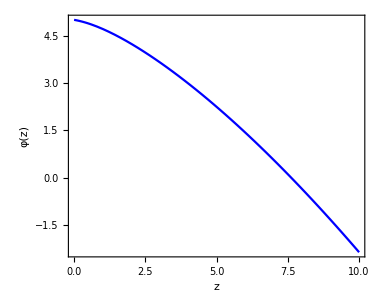

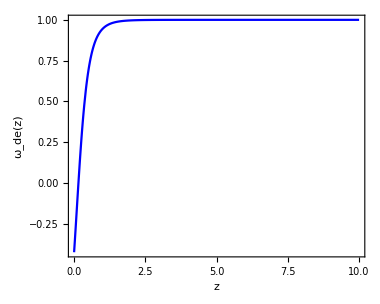

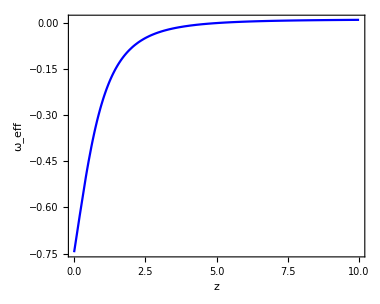

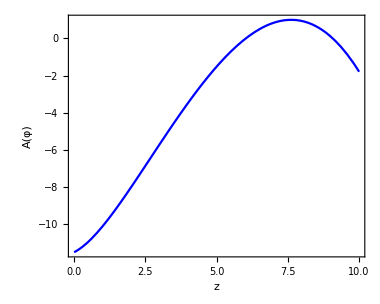

```mathematica
delta=0.672;
c1=2.913;
h0=0.705;
ft1=(100*h0)/Sqrt[1+c1];
ft2=1+3*delta-Sqrt[1+6*delta+9*delta^2+36*(delta-(2/3))];
st=Sqrt[1+6*delta+9*delta^2+36*(delta-(2/3))];
H[z_]:=ft1*((1+z)^(0.25*ft2))*Sqrt[c1+(1+z)^st];
HPrime[z_]=D[H[z],z];
H2[z_]=H[z]^2;
ClearAll[m0,u,ap,mp,l,r,v0,phi,wde,reff,Peff, Ptot, rtot, weff];
m0=(80*10^(-19))/1.22;
u=0.3;
ap=1;
mp=1;
l=1;
r=0.3;
v0=1;
a0=0.1;
eqn=D[phi[z],{z,2}]*H2[z]*(1+z)^2-2*H2[z]*(1+z)* D[phi[z],z]+H[z]*(1+z)^2*HPrime[z]*D[phi[z],z]+2*m0*u*phi[z]+l*phi[z]^3-(ap/mp^2)*r*(1+z)^3*phi[z]==0;
eqn;
TraditionalForm[eqn];
bc={phi[0]==5,phi'[0]==-0.16}; (*,5:-0.5*)
sol=NDSolve[{eqn,bc},phi,{z,0,20}];
Plot[Evaluate[phi[z]/.sol],{z,0,10},Frame->True,AspectRatio->0.8,FrameLabel->{Style["z",Black,FontSize->16],Style["φ(z)", Black, FontSize->18]},LabelStyle->{FontSize->14, Black},FrameStyle->AbsoluteThickness[1.2],PlotStyle->{Blue},ImageSize->380]
dphi[z_]=D[phi[z],z]/.sol;
reff[z_]:=((dphi[z]^2)*(1+z)^2*H2[z])/2+v0+m0*u*(phi[z]/.sol)^2+(l/4)*(phi[z]/.sol)^4;
reff[z];
Peff[z_]:=((dphi[z]^2)*(1+z)^2*H2[z])/2-v0-m0*u*(phi[z]/.sol)^2-(l/4)*(phi[z]/.sol)^4;
Peff[z];
wde[z_]:=Peff[z]/reff[z];
Plot[Evaluate[wde[z]],{z,0,10},Frame->True,AspectRatio->0.8,FrameLabel->{Style["z",Black,FontSize->16],Style[Row[{Subscript["ω","de"],"(z)"}],Black,FontSize->18]},PlotStyle->{Blue},LabelStyle->{FontSize->14},FrameStyle->AbsoluteThickness[1.2], ImageSize->380,PlotRange->{Full,All}]
Ptot[z_]:= (-H[z]^2)/(100*h0)^2+(2*(1+z)*H[z]*HPrime[z])/(3*(100*h0)^2);
rtot[z_] := H[z]^2/(100*h0)^2;
weff[z_] := Ptot[z]/rtot[z];
Plot[Evaluate[weff[z]],{z,0,10},Frame->True,AspectRatio->0.8,FrameLabel->{Style["z",Black,FontSize->16],Style[Row[{Subscript["ω","eff"]}],Black,FontSize->18]},PlotStyle->{Blue},LabelStyle->{FontSize->14},FrameStyle->AbsoluteThickness[1.2],ImageSize->380,PlotRange->{Full,All}]

Aphi[z_]:=1-(ap* (phi[z]/.sol)^2)/(2*mp^2);
Plot[Evaluate[Aphi[z]],{z,0,10},Frame->True,AspectRatio->0.8,FrameLabel->{Style["z",Black,FontSize->16],Style["A(φ)",Black,FontSize->18]},PlotStyle->{Blue},LabelStyle->{FontSize->14},FrameStyle->AbsoluteThickness[1.2],ImageSize->380,PlotRange->{Full,All}]
```